```mathematica
csvPath = "M:\\JI Courses\\Sophomore_Year\\2019_Spring\\VE401\\Proj2\\Codes\\2\\data.csv";
SystemOpen@csvPath
Data = Import[csvPath];
PosDate = Position[Data,"2019-01-01"];
AllDate = Data[[PosDate[[1,1]];;-1,PosDate[[1,2]];;PosDate[[1,2]]]];
For[i=1,i<=Length[AllDate],i++,AllDate[[i]]=DateObject[StringCases[AllDate[[i,1]],x:DatePattern[{"Year","Month","Day"}]:>DateList[x]][[1;;1,1;;3]]][[1]]];
Count1=Tally[AllDate];
```

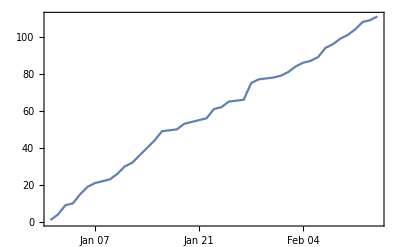

```mathematica
Count2=Count1;
For[i=2,i<=Length[AllDate],i++,
Count2[[i,2]]=Count2[[i-1,2]]+Count2[[i,2]]
];
DateListPlot[Count2]
```